# NZFMR (Near Zero Field Magnetoresistance) of recombination current in Si:P Stochastic Liouville Equation (total spin basis)

```mathematica
Commute[A_,B_]:=A.B-B.A;AntiCommute[A_,B_]:=A.B+B.A
```

```mathematica
μB= 57.88*10^-9 (*eV/mT*);
ℏ= 6.582*10^-16(*eV s*);
g=2.003(* 2.003*);
```

S-T basis (Total Spin)

```mathematica
SLESolveS[a_, kS_, kD_,fudge_,range_List]:=

Module[{},


(* define spin operators*)
sz1=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, 1/2, 0}, {0, 0, 0, -1/2}});
sz2=({{0, -1/2, 0, 0}, {-1/2, 0, 0, 0}, {0, 0, 1/2, 0}, {0, 0, 0, -1/2}});
sx1=1/2({{0, 0, -1/√2, 1/√2}, {0, 0, 1/√2, 1/√2}, {-1/√2, 1/√2, 0, 0}, {1/√2, 1/√2, 0, 0}});
sy1=1/(2 ⅈ)({{0, 0, 1/√2, 1/√2}, {0, 0, -1/√2, 1/√2}, {-1/√2, 1/√2, 0, 0}, {-1/√2, -1/√2, 0, 0}});
sx2=1/2({{0, 0, 1/√2, -1/√2}, {0, 0, 1/√2, 1/√2}, {1/√2, 1/√2, 0, 0}, {-1/√2, 1/√2, 0, 0}});
sy2=1/(2 ⅈ)({{0, 0, -1/√2, -1/√2}, {0, 0, -1/√2, 1/√2}, {1/√2, 1/√2, 0, 0}, {1/√2, -1/√2, 0, 0}});

Sx1= KroneckerProduct[sx1,IdentityMatrix[2]];
Sx2= KroneckerProduct[sx2,IdentityMatrix[2]];
Sy1= KroneckerProduct[sy1,IdentityMatrix[2]];
Sy2= KroneckerProduct[sy2,IdentityMatrix[2]];
Sz1= KroneckerProduct[sz1,IdentityMatrix[2]];
Sz2= KroneckerProduct[sz2,IdentityMatrix[2]];

Ix=KroneckerProduct[IdentityMatrix[4],1/2 PauliMatrix[1]];Iy=KroneckerProduct[IdentityMatrix[4],1/2 PauliMatrix[2]];Iz=KroneckerProduct[IdentityMatrix[4],1/2 PauliMatrix[3]];

(* define singlet and triplet projection operators*)
Ps = DiagonalMatrix[Join[Table[1,{2^1}],Table[0,{4*2^1-2^1}]]];
Pt= DiagonalMatrix[Join[Table[0,{2^1}],Table[1,{4*2^1-2^1}]]];

dim=Dimensions[Ps]⟦1⟧;
equalGen=Table[1,{dim}];

Clear[ρ];
ρ=Table[ρME[i,j],{i,dim},{j,dim}];

(*Solve the SLE for the singlet part of the density matrix for each value of magnetic field Bx *)
ParallelTable[{Bz,fudge*Apply[#&,{(Tr[Ps.Evaluate[ρ/.Flatten[NSolve[(-I/ℏ Commute[g μB Bz * (Sz1 + Sz2 )  +g μB a (Ix.Sx1 + Iy.Sy1 + Iz.Sz1),ρ]-1/2 (kS+kD) AntiCommute[Ps,ρ]-1/2 kD AntiCommute[Pt,ρ])+1/dim DiagonalMatrix[equalGen]==0]//Chop]]])}]//Chop},{Bz,range⟦1⟧,range⟦2⟧,range⟦3⟧}]
]
```

Run the module:

```mathematica
testS = SLESolveS[1,4*10^6, 1*10^6,1,  {-10,10,0.02}];//AbsoluteTiming
```

{7.86493,Null}

Plot

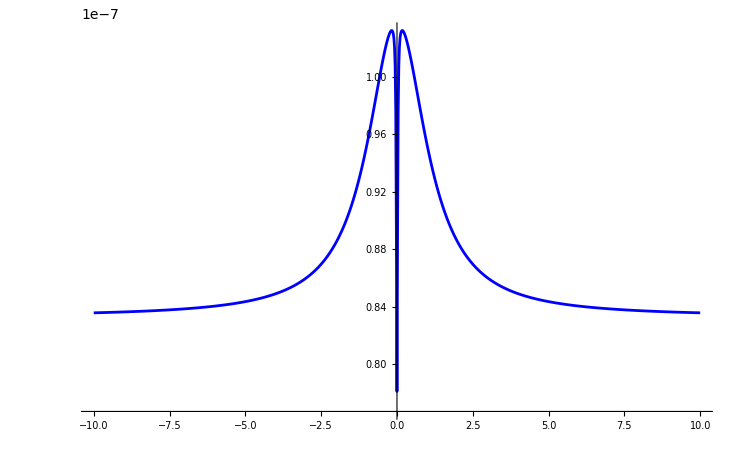

```mathematica
SLEplot1 = ListPlot[{testS}, Joined->True, PlotRange->All, PlotStyle->{{Blue},{Red}}]
```

Just to see what the singlet  and triplet projection operators looks like:

```mathematica
Ps//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Pt//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
g μB Bz * (Sz1 + Sz2 )  +g μB a (Ix.Sx1 + Iy.Sy1 + Iz.Sz1)//MatrixForm
```

(0. | 0. | 0.+2.89834×10^-8 a | 0. | 0. | 0.-4.09887×10^-8 a | 0. | 0.
0. | 0. | 0. | 0.-2.89834×10^-8 a | 0. | 0. | 0.+4.09887×10^-8 a | 0.
0.+2.89834×10^-8 a | 0. | 0. | 0. | 0. | 0.+4.09887×10^-8 a | 0. | 0.
0. | 0.-2.89834×10^-8 a | 0. | 0. | 0. | 0. | 0.+4.09887×10^-8 a | 0.
0. | 0. | 0. | 0. | 2.89834×10^-8 a+1.15934×10^-7 Bz | 0. | 0. | 0.
0.-4.09887×10^-8 a | 0. | 0.+4.09887×10^-8 a | 0. | 0. | -2.89834×10^-8 a+1.15934×10^-7 Bz | 0. | 0.
0. | 0.+4.09887×10^-8 a | 0. | 0.+4.09887×10^-8 a | 0. | 0. | -2.89834×10^-8 a-1.15934×10^-7 Bz | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.89834×10^-8 a-1.15934×10^-7 Bz)

```mathematica
g μB Bz * (Sz1 + Sz2 )  +g μB 1 (Ix.Sx1 + Iy.Sy1 + Iz.Sz1)//Eigenvalues//ToRadicals
```

{2.89834×10^-8-1.15934×10^-7 Bz,2.89834×10^-8+1.15934×10^-7 Bz,1/3 (-2.89834×10^-8+1.15934×10^-7 Bz)-(2^(1/3) (-1.34406×10^-14+6.7203×10^-15 Bz-1.34406×10^-14 Bz^2))/(3 (-3.11644×10^-21+2.33733×10^-21 Bz-2.33733×10^-21 Bz^2+3.11644×10^-21 Bz^3+√(-2.54895×10^-57+5.09789×10^-57 Bz-1.63893×10^-41 Bz^2+5.09789×10^-57 Bz^3-1.63893×10^-41 Bz^4))^(1/3))+1/(3 2^(1/3))(-3.11644×10^-21+2.33733×10^-21 Bz-2.33733×10^-21 Bz^2+3.11644×10^-21 Bz^3+√(-2.54895×10^-57+5.09789×10^-57 Bz-1.63893×10^-41 Bz^2+5.09789×10^-57 Bz^3-1.63893×10^-41 Bz^4))^(1/3),1/3 (-2.89834×10^-8+1.15934×10^-7 Bz)+((1+ⅈ √3) (-1.34406×10^-14+6.7203×10^-15 Bz-1.34406×10^-14 Bz^2))/(3 2^(2/3) (-3.11644×10^-21+2.33733×10^-21 Bz-2.33733×10^-21 Bz^2+3.11644×10^-21 Bz^3+√(-2.54895×10^-57+5.09789×10^-57 Bz-1.63893×10^-41 Bz^2+5.09789×10^-57 Bz^3-1.63893×10^-41 Bz^4))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (-3.11644×10^-21+2.33733×10^-21 Bz-2.33733×10^-21 Bz^2+3.11644×10^-21 Bz^3+√(-2.54895×10^-57+5.09789×10^-57 Bz-1.63893×10^-41 Bz^2+5.09789×10^-57 Bz^3-1.63893×10^-41 Bz^4))^(1/3),1/3 (-2.89834×10^-8+1.15934×10^-7 Bz)+((1-ⅈ √3) (-1.34406×10^-14+6.7203×10^-15 Bz-1.34406×10^-14 Bz^2))/(3 2^(2/3) (-3.11644×10^-21+2.33733×10^-21 Bz-2.33733×10^-21 Bz^2+3.11644×10^-21 Bz^3+√(-2.54895×10^-57+5.09789×10^-57 Bz-1.63893×10^-41 Bz^2+5.09789×10^-57 Bz^3-1.63893×10^-41 Bz^4))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (-3.11644×10^-21+2.33733×10^-21 Bz-2.33733×10^-21 Bz^2+3.11644×10^-21 Bz^3+√(-2.54895×10^-57+5.09789×10^-57 Bz-1.63893×10^-41 Bz^2+5.09789×10^-57 Bz^3-1.63893×10^-41 Bz^4))^(1/3),1/3 (-2.89834×10^-8-1.15934×10^-7 Bz)-(2^(1/3) (-1.34406×10^-14-6.7203×10^-15 Bz-1.34406×10^-14 Bz^2))/(3 (-3.11644×10^-21-2.33733×10^-21 Bz-2.33733×10^-21 Bz^2-3.11644×10^-21 Bz^3+(0.+6.36268×10^-11 ⅈ) √Bz √(3.1105×10^-16+1. Bz) √(4.04837×10^-21+3.91688×10^-52 Bz+4.04837×10^-21 Bz^2))^(1/3))+1/(3 2^(1/3))(-3.11644×10^-21-2.33733×10^-21 Bz-2.33733×10^-21 Bz^2-3.11644×10^-21 Bz^3+(0.+6.36268×10^-11 ⅈ) √Bz √(3.1105×10^-16+1. Bz) √(4.04837×10^-21+3.91688×10^-52 Bz+4.04837×10^-21 Bz^2))^(1/3),1/3 (-2.89834×10^-8-1.15934×10^-7 Bz)+((1+ⅈ √3) (-1.34406×10^-14-6.7203×10^-15 Bz-1.34406×10^-14 Bz^2))/(3 2^(2/3) (-3.11644×10^-21-2.33733×10^-21 Bz-2.33733×10^-21 Bz^2-3.11644×10^-21 Bz^3+(0.+6.36268×10^-11 ⅈ) √Bz √(3.1105×10^-16+1. Bz) √(4.04837×10^-21+3.91688×10^-52 Bz+4.04837×10^-21 Bz^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (-3.11644×10^-21-2.33733×10^-21 Bz-2.33733×10^-21 Bz^2-3.11644×10^-21 Bz^3+(0.+6.36268×10^-11 ⅈ) √Bz √(3.1105×10^-16+1. Bz) √(4.04837×10^-21+3.91688×10^-52 Bz+4.04837×10^-21 Bz^2))^(1/3),1/3 (-2.89834×10^-8-1.15934×10^-7 Bz)+((1-ⅈ √3) (-1.34406×10^-14-6.7203×10^-15 Bz-1.34406×10^-14 Bz^2))/(3 2^(2/3) (-3.11644×10^-21-2.33733×10^-21 Bz-2.33733×10^-21 Bz^2-3.11644×10^-21 Bz^3+(0.+6.36268×10^-11 ⅈ) √Bz √(3.1105×10^-16+1. Bz) √(4.04837×10^-21+3.91688×10^-52 Bz+4.04837×10^-21 Bz^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (-3.11644×10^-21-2.33733×10^-21 Bz-2.33733×10^-21 Bz^2-3.11644×10^-21 Bz^3+(0.+6.36268×10^-11 ⅈ) √Bz √(3.1105×10^-16+1. Bz) √(4.04837×10^-21+3.91688×10^-52 Bz+4.04837×10^-21 Bz^2))^(1/3)}

```mathematica
dim
```

8

```mathematica
equalGen
```

{1,1,1,1,1,1,1,1}

```mathematica
Clear[g, μB, ℏ]
```

```mathematica
eq=(-I/ℏ Commute[g μB Bz * (Sz1 + Sz2 )  +g μB a (Ix.Sx1 + Iy.Sy1 + Iz.Sz1),ρ]-1/2 (kS+kD) AntiCommute[Ps,ρ]-1/2 kD AntiCommute[Pt,ρ])+1/dim DiagonalMatrix[equalGen]//Chop
```

{{1/8-(kD+kS) ρME[1,1]-(ⅈ (-1/4 a g μB ρME[1,3]+(a g μB ρME[1,6])/(2 √2)+1/4 a g μB ρME[3,1]-(a g μB ρME[6,1])/(2 √2)))/ℏ,-((kD+kS) ρME[1,2])-(ⅈ (1/4 a g μB ρME[1,4]-(a g μB ρME[1,7])/(2 √2)+1/4 a g μB ρME[3,2]-(a g μB ρME[6,2])/(2 √2)))/ℏ,-1/2 kD ρME[1,3]-1/2 (kD+kS) ρME[1,3]-(ⅈ (-1/4 a g μB ρME[1,1]-(a g μB ρME[1,6])/(2 √2)+1/4 a g μB ρME[3,3]-(a g μB ρME[6,3])/(2 √2)))/ℏ,-1/2 kD ρME[1,4]-1/2 (kD+kS) ρME[1,4]-(ⅈ (1/4 a g μB ρME[1,2]-(a g μB ρME[1,7])/(2 √2)+1/4 a g μB ρME[3,4]-(a g μB ρME[6,4])/(2 √2)))/ℏ,-1/2 kD ρME[1,5]-1/2 (kD+kS) ρME[1,5]-(ⅈ (-(((a g μB)/4+Bz g μB) ρME[1,5])+1/4 a g μB ρME[3,5]-(a g μB ρME[6,5])/(2 √2)))/ℏ,-1/2 kD ρME[1,6]-1/2 (kD+kS) ρME[1,6]-(ⅈ ((a g μB ρME[1,1])/(2 √2)-(a g μB ρME[1,3])/(2 √2)-(-1/4 a g μB+Bz g μB) ρME[1,6]+1/4 a g μB ρME[3,6]-(a g μB ρME[6,6])/(2 √2)))/ℏ,-1/2 kD ρME[1,7]-1/2 (kD+kS) ρME[1,7]-(ⅈ (-(a g μB ρME[1,2])/(2 √2)-(a g μB ρME[1,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[1,7]+1/4 a g μB ρME[3,7]-(a g μB ρME[6,7])/(2 √2)))/ℏ,-1/2 kD ρME[1,8]-1/2 (kD+kS) ρME[1,8]-(ⅈ (-(((a g μB)/4-Bz g μB) ρME[1,8])+1/4 a g μB ρME[3,8]-(a g μB ρME[6,8])/(2 √2)))/ℏ},{-((kD+kS) ρME[2,1])-(ⅈ (-1/4 a g μB ρME[2,3]+(a g μB ρME[2,6])/(2 √2)-1/4 a g μB ρME[4,1]+(a g μB ρME[7,1])/(2 √2)))/ℏ,1/8-(kD+kS) ρME[2,2]-(ⅈ (1/4 a g μB ρME[2,4]-(a g μB ρME[2,7])/(2 √2)-1/4 a g μB ρME[4,2]+(a g μB ρME[7,2])/(2 √2)))/ℏ,-1/2 kD ρME[2,3]-1/2 (kD+kS) ρME[2,3]-(ⅈ (-1/4 a g μB ρME[2,1]-(a g μB ρME[2,6])/(2 √2)-1/4 a g μB ρME[4,3]+(a g μB ρME[7,3])/(2 √2)))/ℏ,-1/2 kD ρME[2,4]-1/2 (kD+kS) ρME[2,4]-(ⅈ (1/4 a g μB ρME[2,2]-(a g μB ρME[2,7])/(2 √2)-1/4 a g μB ρME[4,4]+(a g μB ρME[7,4])/(2 √2)))/ℏ,-1/2 kD ρME[2,5]-1/2 (kD+kS) ρME[2,5]-(ⅈ (-(((a g μB)/4+Bz g μB) ρME[2,5])-1/4 a g μB ρME[4,5]+(a g μB ρME[7,5])/(2 √2)))/ℏ,-1/2 kD ρME[2,6]-1/2 (kD+kS) ρME[2,6]-(ⅈ ((a g μB ρME[2,1])/(2 √2)-(a g μB ρME[2,3])/(2 √2)-(-1/4 a g μB+Bz g μB) ρME[2,6]-1/4 a g μB ρME[4,6]+(a g μB ρME[7,6])/(2 √2)))/ℏ,-1/2 kD ρME[2,7]-1/2 (kD+kS) ρME[2,7]-(ⅈ (-(a g μB ρME[2,2])/(2 √2)-(a g μB ρME[2,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[2,7]-1/4 a g μB ρME[4,7]+(a g μB ρME[7,7])/(2 √2)))/ℏ,-1/2 kD ρME[2,8]-1/2 (kD+kS) ρME[2,8]-(ⅈ (-(((a g μB)/4-Bz g μB) ρME[2,8])-1/4 a g μB ρME[4,8]+(a g μB ρME[7,8])/(2 √2)))/ℏ},{-1/2 kD ρME[3,1]-1/2 (kD+kS) ρME[3,1]-(ⅈ (1/4 a g μB ρME[1,1]-1/4 a g μB ρME[3,3]+(a g μB ρME[3,6])/(2 √2)+(a g μB ρME[6,1])/(2 √2)))/ℏ,-1/2 kD ρME[3,2]-1/2 (kD+kS) ρME[3,2]-(ⅈ (1/4 a g μB ρME[1,2]+1/4 a g μB ρME[3,4]-(a g μB ρME[3,7])/(2 √2)+(a g μB ρME[6,2])/(2 √2)))/ℏ,1/8-kD ρME[3,3]-(ⅈ (1/4 a g μB ρME[1,3]-1/4 a g μB ρME[3,1]-(a g μB ρME[3,6])/(2 √2)+(a g μB ρME[6,3])/(2 √2)))/ℏ,-kD ρME[3,4]-(ⅈ (1/4 a g μB ρME[1,4]+1/4 a g μB ρME[3,2]-(a g μB ρME[3,7])/(2 √2)+(a g μB ρME[6,4])/(2 √2)))/ℏ,-kD ρME[3,5]-(ⅈ (1/4 a g μB ρME[1,5]-((a g μB)/4+Bz g μB) ρME[3,5]+(a g μB ρME[6,5])/(2 √2)))/ℏ,-kD ρME[3,6]-(ⅈ (1/4 a g μB ρME[1,6]+(a g μB ρME[3,1])/(2 √2)-(a g μB ρME[3,3])/(2 √2)-(-1/4 a g μB+Bz g μB) ρME[3,6]+(a g μB ρME[6,6])/(2 √2)))/ℏ,-kD ρME[3,7]-(ⅈ (1/4 a g μB ρME[1,7]-(a g μB ρME[3,2])/(2 √2)-(a g μB ρME[3,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[3,7]+(a g μB ρME[6,7])/(2 √2)))/ℏ,-kD ρME[3,8]-(ⅈ (1/4 a g μB ρME[1,8]-((a g μB)/4-Bz g μB) ρME[3,8]+(a g μB ρME[6,8])/(2 √2)))/ℏ},{-1/2 kD ρME[4,1]-1/2 (kD+kS) ρME[4,1]-(ⅈ (-1/4 a g μB ρME[2,1]-1/4 a g μB ρME[4,3]+(a g μB ρME[4,6])/(2 √2)+(a g μB ρME[7,1])/(2 √2)))/ℏ,-1/2 kD ρME[4,2]-1/2 (kD+kS) ρME[4,2]-(ⅈ (-1/4 a g μB ρME[2,2]+1/4 a g μB ρME[4,4]-(a g μB ρME[4,7])/(2 √2)+(a g μB ρME[7,2])/(2 √2)))/ℏ,-kD ρME[4,3]-(ⅈ (-1/4 a g μB ρME[2,3]-1/4 a g μB ρME[4,1]-(a g μB ρME[4,6])/(2 √2)+(a g μB ρME[7,3])/(2 √2)))/ℏ,1/8-kD ρME[4,4]-(ⅈ (-1/4 a g μB ρME[2,4]+1/4 a g μB ρME[4,2]-(a g μB ρME[4,7])/(2 √2)+(a g μB ρME[7,4])/(2 √2)))/ℏ,-kD ρME[4,5]-(ⅈ (-1/4 a g μB ρME[2,5]-((a g μB)/4+Bz g μB) ρME[4,5]+(a g μB ρME[7,5])/(2 √2)))/ℏ,-kD ρME[4,6]-(ⅈ (-1/4 a g μB ρME[2,6]+(a g μB ρME[4,1])/(2 √2)-(a g μB ρME[4,3])/(2 √2)-(-1/4 a g μB+Bz g μB) ρME[4,6]+(a g μB ρME[7,6])/(2 √2)))/ℏ,-kD ρME[4,7]-(ⅈ (-1/4 a g μB ρME[2,7]-(a g μB ρME[4,2])/(2 √2)-(a g μB ρME[4,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[4,7]+(a g μB ρME[7,7])/(2 √2)))/ℏ,-kD ρME[4,8]-(ⅈ (-1/4 a g μB ρME[2,8]-((a g μB)/4-Bz g μB) ρME[4,8]+(a g μB ρME[7,8])/(2 √2)))/ℏ},{-1/2 kD ρME[5,1]-1/2 (kD+kS) ρME[5,1]-(ⅈ (((a g μB)/4+Bz g μB) ρME[5,1]-1/4 a g μB ρME[5,3]+(a g μB ρME[5,6])/(2 √2)))/ℏ,-1/2 kD ρME[5,2]-1/2 (kD+kS) ρME[5,2]-(ⅈ (((a g μB)/4+Bz g μB) ρME[5,2]+1/4 a g μB ρME[5,4]-(a g μB ρME[5,7])/(2 √2)))/ℏ,-kD ρME[5,3]-(ⅈ (-1/4 a g μB ρME[5,1]+((a g μB)/4+Bz g μB) ρME[5,3]-(a g μB ρME[5,6])/(2 √2)))/ℏ,-kD ρME[5,4]-(ⅈ (1/4 a g μB ρME[5,2]+((a g μB)/4+Bz g μB) ρME[5,4]-(a g μB ρME[5,7])/(2 √2)))/ℏ,1/8-kD ρME[5,5],-kD ρME[5,6]-(ⅈ ((a g μB ρME[5,1])/(2 √2)-(a g μB ρME[5,3])/(2 √2)-(-1/4 a g μB+Bz g μB) ρME[5,6]+((a g μB)/4+Bz g μB) ρME[5,6]))/ℏ,-kD ρME[5,7]-(ⅈ (-(a g μB ρME[5,2])/(2 √2)-(a g μB ρME[5,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[5,7]+((a g μB)/4+Bz g μB) ρME[5,7]))/ℏ,-kD ρME[5,8]-(ⅈ (-(((a g μB)/4-Bz g μB) ρME[5,8])+((a g μB)/4+Bz g μB) ρME[5,8]))/ℏ},{-1/2 kD ρME[6,1]-1/2 (kD+kS) ρME[6,1]-(ⅈ (-(a g μB ρME[1,1])/(2 √2)+(a g μB ρME[3,1])/(2 √2)+(-1/4 a g μB+Bz g μB) ρME[6,1]-1/4 a g μB ρME[6,3]+(a g μB ρME[6,6])/(2 √2)))/ℏ,-1/2 kD ρME[6,2]-1/2 (kD+kS) ρME[6,2]-(ⅈ (-(a g μB ρME[1,2])/(2 √2)+(a g μB ρME[3,2])/(2 √2)+(-1/4 a g μB+Bz g μB) ρME[6,2]+1/4 a g μB ρME[6,4]-(a g μB ρME[6,7])/(2 √2)))/ℏ,-kD ρME[6,3]-(ⅈ (-(a g μB ρME[1,3])/(2 √2)+(a g μB ρME[3,3])/(2 √2)-1/4 a g μB ρME[6,1]+(-1/4 a g μB+Bz g μB) ρME[6,3]-(a g μB ρME[6,6])/(2 √2)))/ℏ,-kD ρME[6,4]-(ⅈ (-(a g μB ρME[1,4])/(2 √2)+(a g μB ρME[3,4])/(2 √2)+1/4 a g μB ρME[6,2]+(-1/4 a g μB+Bz g μB) ρME[6,4]-(a g μB ρME[6,7])/(2 √2)))/ℏ,-kD ρME[6,5]-(ⅈ (-(a g μB ρME[1,5])/(2 √2)+(a g μB ρME[3,5])/(2 √2)+(-1/4 a g μB+Bz g μB) ρME[6,5]-((a g μB)/4+Bz g μB) ρME[6,5]))/ℏ,1/8-(ⅈ (-(a g μB ρME[1,6])/(2 √2)+(a g μB ρME[3,6])/(2 √2)+(a g μB ρME[6,1])/(2 √2)-(a g μB ρME[6,3])/(2 √2)))/ℏ-kD ρME[6,6],-kD ρME[6,7]-(ⅈ (-(a g μB ρME[1,7])/(2 √2)+(a g μB ρME[3,7])/(2 √2)-(a g μB ρME[6,2])/(2 √2)-(a g μB ρME[6,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[6,7]+(-1/4 a g μB+Bz g μB) ρME[6,7]))/ℏ,-kD ρME[6,8]-(ⅈ (-(a g μB ρME[1,8])/(2 √2)+(a g μB ρME[3,8])/(2 √2)-((a g μB)/4-Bz g μB) ρME[6,8]+(-1/4 a g μB+Bz g μB) ρME[6,8]))/ℏ},{-1/2 kD ρME[7,1]-1/2 (kD+kS) ρME[7,1]-(ⅈ ((a g μB ρME[2,1])/(2 √2)+(a g μB ρME[4,1])/(2 √2)+(-1/4 a g μB-Bz g μB) ρME[7,1]-1/4 a g μB ρME[7,3]+(a g μB ρME[7,6])/(2 √2)))/ℏ,-1/2 kD ρME[7,2]-1/2 (kD+kS) ρME[7,2]-(ⅈ ((a g μB ρME[2,2])/(2 √2)+(a g μB ρME[4,2])/(2 √2)+(-1/4 a g μB-Bz g μB) ρME[7,2]+1/4 a g μB ρME[7,4]-(a g μB ρME[7,7])/(2 √2)))/ℏ,-kD ρME[7,3]-(ⅈ ((a g μB ρME[2,3])/(2 √2)+(a g μB ρME[4,3])/(2 √2)-1/4 a g μB ρME[7,1]+(-1/4 a g μB-Bz g μB) ρME[7,3]-(a g μB ρME[7,6])/(2 √2)))/ℏ,-kD ρME[7,4]-(ⅈ ((a g μB ρME[2,4])/(2 √2)+(a g μB ρME[4,4])/(2 √2)+1/4 a g μB ρME[7,2]+(-1/4 a g μB-Bz g μB) ρME[7,4]-(a g μB ρME[7,7])/(2 √2)))/ℏ,-kD ρME[7,5]-(ⅈ ((a g μB ρME[2,5])/(2 √2)+(a g μB ρME[4,5])/(2 √2)+(-1/4 a g μB-Bz g μB) ρME[7,5]-((a g μB)/4+Bz g μB) ρME[7,5]))/ℏ,-kD ρME[7,6]-(ⅈ ((a g μB ρME[2,6])/(2 √2)+(a g μB ρME[4,6])/(2 √2)+(a g μB ρME[7,1])/(2 √2)-(a g μB ρME[7,3])/(2 √2)+(-1/4 a g μB-Bz g μB) ρME[7,6]-(-1/4 a g μB+Bz g μB) ρME[7,6]))/ℏ,1/8-(ⅈ ((a g μB ρME[2,7])/(2 √2)+(a g μB ρME[4,7])/(2 √2)-(a g μB ρME[7,2])/(2 √2)-(a g μB ρME[7,4])/(2 √2)))/ℏ-kD ρME[7,7],-kD ρME[7,8]-(ⅈ ((a g μB ρME[2,8])/(2 √2)+(a g μB ρME[4,8])/(2 √2)+(-1/4 a g μB-Bz g μB) ρME[7,8]-((a g μB)/4-Bz g μB) ρME[7,8]))/ℏ},{-1/2 kD ρME[8,1]-1/2 (kD+kS) ρME[8,1]-(ⅈ (((a g μB)/4-Bz g μB) ρME[8,1]-1/4 a g μB ρME[8,3]+(a g μB ρME[8,6])/(2 √2)))/ℏ,-1/2 kD ρME[8,2]-1/2 (kD+kS) ρME[8,2]-(ⅈ (((a g μB)/4-Bz g μB) ρME[8,2]+1/4 a g μB ρME[8,4]-(a g μB ρME[8,7])/(2 √2)))/ℏ,-kD ρME[8,3]-(ⅈ (-1/4 a g μB ρME[8,1]+((a g μB)/4-Bz g μB) ρME[8,3]-(a g μB ρME[8,6])/(2 √2)))/ℏ,-kD ρME[8,4]-(ⅈ (1/4 a g μB ρME[8,2]+((a g μB)/4-Bz g μB) ρME[8,4]-(a g μB ρME[8,7])/(2 √2)))/ℏ,-kD ρME[8,5]-(ⅈ (((a g μB)/4-Bz g μB) ρME[8,5]-((a g μB)/4+Bz g μB) ρME[8,5]))/ℏ,-kD ρME[8,6]-(ⅈ ((a g μB ρME[8,1])/(2 √2)-(a g μB ρME[8,3])/(2 √2)+((a g μB)/4-Bz g μB) ρME[8,6]-(-1/4 a g μB+Bz g μB) ρME[8,6]))/ℏ,-kD ρME[8,7]-(ⅈ (-(a g μB ρME[8,2])/(2 √2)-(a g μB ρME[8,4])/(2 √2)-(-1/4 a g μB-Bz g μB) ρME[8,7]+((a g μB)/4-Bz g μB) ρME[8,7]))/ℏ,1/8-kD ρME[8,8]}}

```mathematica
eq/.{Bz->1, a->1, ℏ->1, g->1, μB->1, kS->1, kD->1}
```

{{1/8-2 ρME[1,1]-ⅈ (-1/4 ρME[1,3]+ρME[1,6]/(2 √2)+1/4 ρME[3,1]-ρME[6,1]/(2 √2)),-2 ρME[1,2]-ⅈ (1/4 ρME[1,4]-ρME[1,7]/(2 √2)+1/4 ρME[3,2]-ρME[6,2]/(2 √2)),-3/2 ρME[1,3]-ⅈ (-1/4 ρME[1,1]-ρME[1,6]/(2 √2)+1/4 ρME[3,3]-ρME[6,3]/(2 √2)),-3/2 ρME[1,4]-ⅈ (1/4 ρME[1,2]-ρME[1,7]/(2 √2)+1/4 ρME[3,4]-ρME[6,4]/(2 √2)),-3/2 ρME[1,5]-ⅈ (-5/4 ρME[1,5]+1/4 ρME[3,5]-ρME[6,5]/(2 √2)),-3/2 ρME[1,6]-ⅈ (ρME[1,1]/(2 √2)-ρME[1,3]/(2 √2)-3/4 ρME[1,6]+1/4 ρME[3,6]-ρME[6,6]/(2 √2)),-3/2 ρME[1,7]-ⅈ (-ρME[1,2]/(2 √2)-ρME[1,4]/(2 √2)+5/4 ρME[1,7]+1/4 ρME[3,7]-ρME[6,7]/(2 √2)),-3/2 ρME[1,8]-ⅈ (3/4 ρME[1,8]+1/4 ρME[3,8]-ρME[6,8]/(2 √2))},{-2 ρME[2,1]-ⅈ (-1/4 ρME[2,3]+ρME[2,6]/(2 √2)-1/4 ρME[4,1]+ρME[7,1]/(2 √2)),1/8-2 ρME[2,2]-ⅈ (1/4 ρME[2,4]-ρME[2,7]/(2 √2)-1/4 ρME[4,2]+ρME[7,2]/(2 √2)),-3/2 ρME[2,3]-ⅈ (-1/4 ρME[2,1]-ρME[2,6]/(2 √2)-1/4 ρME[4,3]+ρME[7,3]/(2 √2)),-3/2 ρME[2,4]-ⅈ (1/4 ρME[2,2]-ρME[2,7]/(2 √2)-1/4 ρME[4,4]+ρME[7,4]/(2 √2)),-3/2 ρME[2,5]-ⅈ (-5/4 ρME[2,5]-1/4 ρME[4,5]+ρME[7,5]/(2 √2)),-3/2 ρME[2,6]-ⅈ (ρME[2,1]/(2 √2)-ρME[2,3]/(2 √2)-3/4 ρME[2,6]-1/4 ρME[4,6]+ρME[7,6]/(2 √2)),-3/2 ρME[2,7]-ⅈ (-ρME[2,2]/(2 √2)-ρME[2,4]/(2 √2)+5/4 ρME[2,7]-1/4 ρME[4,7]+ρME[7,7]/(2 √2)),-3/2 ρME[2,8]-ⅈ (3/4 ρME[2,8]-1/4 ρME[4,8]+ρME[7,8]/(2 √2))},{-3/2 ρME[3,1]-ⅈ (1/4 ρME[1,1]-1/4 ρME[3,3]+ρME[3,6]/(2 √2)+ρME[6,1]/(2 √2)),-3/2 ρME[3,2]-ⅈ (1/4 ρME[1,2]+1/4 ρME[3,4]-ρME[3,7]/(2 √2)+ρME[6,2]/(2 √2)),1/8-ρME[3,3]-ⅈ (1/4 ρME[1,3]-1/4 ρME[3,1]-ρME[3,6]/(2 √2)+ρME[6,3]/(2 √2)),-ρME[3,4]-ⅈ (1/4 ρME[1,4]+1/4 ρME[3,2]-ρME[3,7]/(2 √2)+ρME[6,4]/(2 √2)),-ρME[3,5]-ⅈ (1/4 ρME[1,5]-5/4 ρME[3,5]+ρME[6,5]/(2 √2)),-ρME[3,6]-ⅈ (1/4 ρME[1,6]+ρME[3,1]/(2 √2)-ρME[3,3]/(2 √2)-3/4 ρME[3,6]+ρME[6,6]/(2 √2)),-ρME[3,7]-ⅈ (1/4 ρME[1,7]-ρME[3,2]/(2 √2)-ρME[3,4]/(2 √2)+5/4 ρME[3,7]+ρME[6,7]/(2 √2)),-ρME[3,8]-ⅈ (1/4 ρME[1,8]+3/4 ρME[3,8]+ρME[6,8]/(2 √2))},{-3/2 ρME[4,1]-ⅈ (-1/4 ρME[2,1]-1/4 ρME[4,3]+ρME[4,6]/(2 √2)+ρME[7,1]/(2 √2)),-3/2 ρME[4,2]-ⅈ (-1/4 ρME[2,2]+1/4 ρME[4,4]-ρME[4,7]/(2 √2)+ρME[7,2]/(2 √2)),-ρME[4,3]-ⅈ (-1/4 ρME[2,3]-1/4 ρME[4,1]-ρME[4,6]/(2 √2)+ρME[7,3]/(2 √2)),1/8-ρME[4,4]-ⅈ (-1/4 ρME[2,4]+1/4 ρME[4,2]-ρME[4,7]/(2 √2)+ρME[7,4]/(2 √2)),-ρME[4,5]-ⅈ (-1/4 ρME[2,5]-5/4 ρME[4,5]+ρME[7,5]/(2 √2)),-ρME[4,6]-ⅈ (-1/4 ρME[2,6]+ρME[4,1]/(2 √2)-ρME[4,3]/(2 √2)-3/4 ρME[4,6]+ρME[7,6]/(2 √2)),-ρME[4,7]-ⅈ (-1/4 ρME[2,7]-ρME[4,2]/(2 √2)-ρME[4,4]/(2 √2)+5/4 ρME[4,7]+ρME[7,7]/(2 √2)),-ρME[4,8]-ⅈ (-1/4 ρME[2,8]+3/4 ρME[4,8]+ρME[7,8]/(2 √2))},{-3/2 ρME[5,1]-ⅈ (5/4 ρME[5,1]-1/4 ρME[5,3]+ρME[5,6]/(2 √2)),-3/2 ρME[5,2]-ⅈ (5/4 ρME[5,2]+1/4 ρME[5,4]-ρME[5,7]/(2 √2)),-ρME[5,3]-ⅈ (-1/4 ρME[5,1]+5/4 ρME[5,3]-ρME[5,6]/(2 √2)),-ρME[5,4]-ⅈ (1/4 ρME[5,2]+5/4 ρME[5,4]-ρME[5,7]/(2 √2)),1/8-ρME[5,5],-ⅈ (ρME[5,1]/(2 √2)-ρME[5,3]/(2 √2)+1/2 ρME[5,6])-ρME[5,6],-ρME[5,7]-ⅈ (-ρME[5,2]/(2 √2)-ρME[5,4]/(2 √2)+5/2 ρME[5,7]),(-1-2 ⅈ) ρME[5,8]},{-3/2 ρME[6,1]-ⅈ (-ρME[1,1]/(2 √2)+ρME[3,1]/(2 √2)+3/4 ρME[6,1]-1/4 ρME[6,3]+ρME[6,6]/(2 √2)),-3/2 ρME[6,2]-ⅈ (-ρME[1,2]/(2 √2)+ρME[3,2]/(2 √2)+3/4 ρME[6,2]+1/4 ρME[6,4]-ρME[6,7]/(2 √2)),-ρME[6,3]-ⅈ (-ρME[1,3]/(2 √2)+ρME[3,3]/(2 √2)-1/4 ρME[6,1]+3/4 ρME[6,3]-ρME[6,6]/(2 √2)),-ρME[6,4]-ⅈ (-ρME[1,4]/(2 √2)+ρME[3,4]/(2 √2)+1/4 ρME[6,2]+3/4 ρME[6,4]-ρME[6,7]/(2 √2)),-ⅈ (-ρME[1,5]/(2 √2)+ρME[3,5]/(2 √2)-1/2 ρME[6,5])-ρME[6,5],1/8-ⅈ (-ρME[1,6]/(2 √2)+ρME[3,6]/(2 √2)+ρME[6,1]/(2 √2)-ρME[6,3]/(2 √2))-ρME[6,6],-ρME[6,7]-ⅈ (-ρME[1,7]/(2 √2)+ρME[3,7]/(2 √2)-ρME[6,2]/(2 √2)-ρME[6,4]/(2 √2)+2 ρME[6,7]),-ρME[6,8]-ⅈ (-ρME[1,8]/(2 √2)+ρME[3,8]/(2 √2)+3/2 ρME[6,8])},{-3/2 ρME[7,1]-ⅈ (ρME[2,1]/(2 √2)+ρME[4,1]/(2 √2)-5/4 ρME[7,1]-1/4 ρME[7,3]+ρME[7,6]/(2 √2)),-3/2 ρME[7,2]-ⅈ (ρME[2,2]/(2 √2)+ρME[4,2]/(2 √2)-5/4 ρME[7,2]+1/4 ρME[7,4]-ρME[7,7]/(2 √2)),-ρME[7,3]-ⅈ (ρME[2,3]/(2 √2)+ρME[4,3]/(2 √2)-1/4 ρME[7,1]-5/4 ρME[7,3]-ρME[7,6]/(2 √2)),-ρME[7,4]-ⅈ (ρME[2,4]/(2 √2)+ρME[4,4]/(2 √2)+1/4 ρME[7,2]-5/4 ρME[7,4]-ρME[7,7]/(2 √2)),-ⅈ (ρME[2,5]/(2 √2)+ρME[4,5]/(2 √2)-5/2 ρME[7,5])-ρME[7,5],-ⅈ (ρME[2,6]/(2 √2)+ρME[4,6]/(2 √2)+ρME[7,1]/(2 √2)-ρME[7,3]/(2 √2)-2 ρME[7,6])-ρME[7,6],1/8-ⅈ (ρME[2,7]/(2 √2)+ρME[4,7]/(2 √2)-ρME[7,2]/(2 √2)-ρME[7,4]/(2 √2))-ρME[7,7],-ⅈ (ρME[2,8]/(2 √2)+ρME[4,8]/(2 √2)-1/2 ρME[7,8])-ρME[7,8]},{-3/2 ρME[8,1]-ⅈ (-3/4 ρME[8,1]-1/4 ρME[8,3]+ρME[8,6]/(2 √2)),-3/2 ρME[8,2]-ⅈ (-3/4 ρME[8,2]+1/4 ρME[8,4]-ρME[8,7]/(2 √2)),-ρME[8,3]-ⅈ (-1/4 ρME[8,1]-3/4 ρME[8,3]-ρME[8,6]/(2 √2)),-ρME[8,4]-ⅈ (1/4 ρME[8,2]-3/4 ρME[8,4]-ρME[8,7]/(2 √2)),(-1+2 ⅈ) ρME[8,5],-ⅈ (ρME[8,1]/(2 √2)-ρME[8,3]/(2 √2)-3/2 ρME[8,6])-ρME[8,6],-ⅈ (-ρME[8,2]/(2 √2)-ρME[8,4]/(2 √2)+1/2 ρME[8,7])-ρME[8,7],1/8-ρME[8,8]}}

```mathematica
(*Example symbolic expression*)expr[a_,b_,c_]:=eq;

(*Convert to C syntax as a string*)
cExpr=ToString[CForm@expr[Symbol["a"],Symbol["b"],Symbol["c"]],InputForm];
```

```mathematica
cExpr
```

List(0.125 - (kD + kS)*ρME(1,1) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(1,3)) + (a*g*μB*ρME(1,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(3,1))/4. - (a*g*μB*ρME(6,1))/(2.*Sqrt(2))))/ℏ,-((kD + kS)*ρME(1,2)) - (Complex(0,1)*((a*g*μB*ρME(1,4))/4. - (a*g*μB*ρME(1,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(3,2))/4. - (a*g*μB*ρME(6,2))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(1,3)) - ((kD + kS)*ρME(1,3))/2. - (Complex(0,1)*(-0.25*(a*g*μB*ρME(1,1)) - (a*g*μB*ρME(1,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(3,3))/4. - (a*g*μB*ρME(6,3))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(1,4)) - ((kD + kS)*ρME(1,4))/2. - (Complex(0,1)*((a*g*μB*ρME(1,2))/4. - (a*g*μB*ρME(1,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(3,4))/4. - (a*g*μB*ρME(6,4))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(1,5)) - ((kD + kS)*ρME(1,5))/2. - (Complex(0,1)*(-(((a*g*μB)/4. + Bz*g*μB)*ρME(1,5)) + (a*g*μB*ρME(3,5))/4. - (a*g*μB*ρME(6,5))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(1,6)) - ((kD + kS)*ρME(1,6))/2. - (Complex(0,1)*((a*g*μB*ρME(1,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(1,3))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(1,6) + (a*g*μB*ρME(3,6))/4. - (a*g*μB*ρME(6,6))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(1,7)) - ((kD + kS)*ρME(1,7))/2. - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,2))/Sqrt(2) - (a*g*μB*ρME(1,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(1,7) + (a*g*μB*ρME(3,7))/4. - (a*g*μB*ρME(6,7))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(1,8)) - ((kD + kS)*ρME(1,8))/2. - (Complex(0,1)*(-(((a*g*μB)/4. - Bz*g*μB)*ρME(1,8)) + (a*g*μB*ρME(3,8))/4. - (a*g*μB*ρME(6,8))/(2.*Sqrt(2))))/ℏ,-((kD + kS)*ρME(2,1)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,3)) + (a*g*μB*ρME(2,6))/(2.*Sqrt(2)) - (a*g*μB*ρME(4,1))/4. + (a*g*μB*ρME(7,1))/(2.*Sqrt(2))))/ℏ,0.125 - (kD + kS)*ρME(2,2) - (Complex(0,1)*((a*g*μB*ρME(2,4))/4. - (a*g*μB*ρME(2,7))/(2.*Sqrt(2)) - (a*g*μB*ρME(4,2))/4. + (a*g*μB*ρME(7,2))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(2,3)) - ((kD + kS)*ρME(2,3))/2. - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,1)) - (a*g*μB*ρME(2,6))/(2.*Sqrt(2)) - (a*g*μB*ρME(4,3))/4. + (a*g*μB*ρME(7,3))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(2,4)) - ((kD + kS)*ρME(2,4))/2. - (Complex(0,1)*((a*g*μB*ρME(2,2))/4. - (a*g*μB*ρME(2,7))/(2.*Sqrt(2)) - (a*g*μB*ρME(4,4))/4. + (a*g*μB*ρME(7,4))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(2,5)) - ((kD + kS)*ρME(2,5))/2. - (Complex(0,1)*(-(((a*g*μB)/4. + Bz*g*μB)*ρME(2,5)) - (a*g*μB*ρME(4,5))/4. + (a*g*μB*ρME(7,5))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(2,6)) - ((kD + kS)*ρME(2,6))/2. - (Complex(0,1)*((a*g*μB*ρME(2,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(2,3))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(2,6) - (a*g*μB*ρME(4,6))/4. + (a*g*μB*ρME(7,6))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(2,7)) - ((kD + kS)*ρME(2,7))/2. - (Complex(0,1)*(-0.5*(a*g*μB*ρME(2,2))/Sqrt(2) - (a*g*μB*ρME(2,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(2,7) - (a*g*μB*ρME(4,7))/4. + (a*g*μB*ρME(7,7))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(2,8)) - ((kD + kS)*ρME(2,8))/2. - (Complex(0,1)*(-(((a*g*μB)/4. - Bz*g*μB)*ρME(2,8)) - (a*g*μB*ρME(4,8))/4. + (a*g*μB*ρME(7,8))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(3,1)) - ((kD + kS)*ρME(3,1))/2. - (Complex(0,1)*((a*g*μB*ρME(1,1))/4. - (a*g*μB*ρME(3,3))/4. + (a*g*μB*ρME(3,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(6,1))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(3,2)) - ((kD + kS)*ρME(3,2))/2. - (Complex(0,1)*((a*g*μB*ρME(1,2))/4. + (a*g*μB*ρME(3,4))/4. - (a*g*μB*ρME(3,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(6,2))/(2.*Sqrt(2))))/ℏ,0.125 - kD*ρME(3,3) - (Complex(0,1)*((a*g*μB*ρME(1,3))/4. - (a*g*μB*ρME(3,1))/4. - (a*g*μB*ρME(3,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(6,3))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(3,4)) - (Complex(0,1)*((a*g*μB*ρME(1,4))/4. + (a*g*μB*ρME(3,2))/4. - (a*g*μB*ρME(3,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(6,4))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(3,5)) - (Complex(0,1)*((a*g*μB*ρME(1,5))/4. - ((a*g*μB)/4. + Bz*g*μB)*ρME(3,5) + (a*g*μB*ρME(6,5))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(3,6)) - (Complex(0,1)*((a*g*μB*ρME(1,6))/4. + (a*g*μB*ρME(3,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(3,3))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(3,6) + (a*g*μB*ρME(6,6))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(3,7)) - (Complex(0,1)*((a*g*μB*ρME(1,7))/4. - (a*g*μB*ρME(3,2))/(2.*Sqrt(2)) - (a*g*μB*ρME(3,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(3,7) + (a*g*μB*ρME(6,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(3,8)) - (Complex(0,1)*((a*g*μB*ρME(1,8))/4. - ((a*g*μB)/4. - Bz*g*μB)*ρME(3,8) + (a*g*μB*ρME(6,8))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(4,1)) - ((kD + kS)*ρME(4,1))/2. - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,1)) - (a*g*μB*ρME(4,3))/4. + (a*g*μB*ρME(4,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(7,1))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(4,2)) - ((kD + kS)*ρME(4,2))/2. - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,2)) + (a*g*μB*ρME(4,4))/4. - (a*g*μB*ρME(4,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(7,2))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(4,3)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,3)) - (a*g*μB*ρME(4,1))/4. - (a*g*μB*ρME(4,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(7,3))/(2.*Sqrt(2))))/ℏ,0.125 - kD*ρME(4,4) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,4)) + (a*g*μB*ρME(4,2))/4. - (a*g*μB*ρME(4,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(7,4))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(4,5)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,5)) - ((a*g*μB)/4. + Bz*g*μB)*ρME(4,5) + (a*g*μB*ρME(7,5))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(4,6)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,6)) + (a*g*μB*ρME(4,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(4,3))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(4,6) + (a*g*μB*ρME(7,6))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(4,7)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,7)) - (a*g*μB*ρME(4,2))/(2.*Sqrt(2)) - (a*g*μB*ρME(4,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(4,7) + (a*g*μB*ρME(7,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(4,8)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(2,8)) - ((a*g*μB)/4. - Bz*g*μB)*ρME(4,8) + (a*g*μB*ρME(7,8))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(5,1)) - ((kD + kS)*ρME(5,1))/2. - (Complex(0,1)*(((a*g*μB)/4. + Bz*g*μB)*ρME(5,1) - (a*g*μB*ρME(5,3))/4. + (a*g*μB*ρME(5,6))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(5,2)) - ((kD + kS)*ρME(5,2))/2. - (Complex(0,1)*(((a*g*μB)/4. + Bz*g*μB)*ρME(5,2) + (a*g*μB*ρME(5,4))/4. - (a*g*μB*ρME(5,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(5,3)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(5,1)) + ((a*g*μB)/4. + Bz*g*μB)*ρME(5,3) - (a*g*μB*ρME(5,6))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(5,4)) - (Complex(0,1)*((a*g*μB*ρME(5,2))/4. + ((a*g*μB)/4. + Bz*g*μB)*ρME(5,4) - (a*g*μB*ρME(5,7))/(2.*Sqrt(2))))/ℏ,0.125 - kD*ρME(5,5),-(kD*ρME(5,6)) - (Complex(0,1)*((a*g*μB*ρME(5,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(5,3))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(5,6) + ((a*g*μB)/4. + Bz*g*μB)*ρME(5,6)))/ℏ,-(kD*ρME(5,7)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(5,2))/Sqrt(2) - (a*g*μB*ρME(5,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(5,7) + ((a*g*μB)/4. + Bz*g*μB)*ρME(5,7)))/ℏ,-(kD*ρME(5,8)) - (Complex(0,1)*(-(((a*g*μB)/4. - Bz*g*μB)*ρME(5,8)) + ((a*g*μB)/4. + Bz*g*μB)*ρME(5,8)))/ℏ,-0.5*(kD*ρME(6,1)) - ((kD + kS)*ρME(6,1))/2. - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,1))/Sqrt(2) + (a*g*μB*ρME(3,1))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,1) - (a*g*μB*ρME(6,3))/4. + (a*g*μB*ρME(6,6))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(6,2)) - ((kD + kS)*ρME(6,2))/2. - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,2))/Sqrt(2) + (a*g*μB*ρME(3,2))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,2) + (a*g*μB*ρME(6,4))/4. - (a*g*μB*ρME(6,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(6,3)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,3))/Sqrt(2) + (a*g*μB*ρME(3,3))/(2.*Sqrt(2)) - (a*g*μB*ρME(6,1))/4. + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,3) - (a*g*μB*ρME(6,6))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(6,4)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,4))/Sqrt(2) + (a*g*μB*ρME(3,4))/(2.*Sqrt(2)) + (a*g*μB*ρME(6,2))/4. + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,4) - (a*g*μB*ρME(6,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(6,5)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,5))/Sqrt(2) + (a*g*μB*ρME(3,5))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,5) - ((a*g*μB)/4. + Bz*g*μB)*ρME(6,5)))/ℏ,0.125 - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,6))/Sqrt(2) + (a*g*μB*ρME(3,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(6,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(6,3))/(2.*Sqrt(2))))/ℏ - kD*ρME(6,6),-(kD*ρME(6,7)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,7))/Sqrt(2) + (a*g*μB*ρME(3,7))/(2.*Sqrt(2)) - (a*g*μB*ρME(6,2))/(2.*Sqrt(2)) - (a*g*μB*ρME(6,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(6,7) + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,7)))/ℏ,-(kD*ρME(6,8)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(1,8))/Sqrt(2) + (a*g*μB*ρME(3,8))/(2.*Sqrt(2)) - ((a*g*μB)/4. - Bz*g*μB)*ρME(6,8) + (-0.25*(a*g*μB) + Bz*g*μB)*ρME(6,8)))/ℏ,-0.5*(kD*ρME(7,1)) - ((kD + kS)*ρME(7,1))/2. - (Complex(0,1)*((a*g*μB*ρME(2,1))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,1))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,1) - (a*g*μB*ρME(7,3))/4. + (a*g*μB*ρME(7,6))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(7,2)) - ((kD + kS)*ρME(7,2))/2. - (Complex(0,1)*((a*g*μB*ρME(2,2))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,2))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,2) + (a*g*μB*ρME(7,4))/4. - (a*g*μB*ρME(7,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(7,3)) - (Complex(0,1)*((a*g*μB*ρME(2,3))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,3))/(2.*Sqrt(2)) - (a*g*μB*ρME(7,1))/4. + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,3) - (a*g*μB*ρME(7,6))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(7,4)) - (Complex(0,1)*((a*g*μB*ρME(2,4))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,4))/(2.*Sqrt(2)) + (a*g*μB*ρME(7,2))/4. + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,4) - (a*g*μB*ρME(7,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(7,5)) - (Complex(0,1)*((a*g*μB*ρME(2,5))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,5))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,5) - ((a*g*μB)/4. + Bz*g*μB)*ρME(7,5)))/ℏ,-(kD*ρME(7,6)) - (Complex(0,1)*((a*g*μB*ρME(2,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,6))/(2.*Sqrt(2)) + (a*g*μB*ρME(7,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(7,3))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,6) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(7,6)))/ℏ,0.125 - (Complex(0,1)*((a*g*μB*ρME(2,7))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,7))/(2.*Sqrt(2)) - (a*g*μB*ρME(7,2))/(2.*Sqrt(2)) - (a*g*μB*ρME(7,4))/(2.*Sqrt(2))))/ℏ - kD*ρME(7,7),-(kD*ρME(7,8)) - (Complex(0,1)*((a*g*μB*ρME(2,8))/(2.*Sqrt(2)) + (a*g*μB*ρME(4,8))/(2.*Sqrt(2)) + (-0.25*(a*g*μB) - Bz*g*μB)*ρME(7,8) - ((a*g*μB)/4. - Bz*g*μB)*ρME(7,8)))/ℏ,-0.5*(kD*ρME(8,1)) - ((kD + kS)*ρME(8,1))/2. - (Complex(0,1)*(((a*g*μB)/4. - Bz*g*μB)*ρME(8,1) - (a*g*μB*ρME(8,3))/4. + (a*g*μB*ρME(8,6))/(2.*Sqrt(2))))/ℏ,-0.5*(kD*ρME(8,2)) - ((kD + kS)*ρME(8,2))/2. - (Complex(0,1)*(((a*g*μB)/4. - Bz*g*μB)*ρME(8,2) + (a*g*μB*ρME(8,4))/4. - (a*g*μB*ρME(8,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(8,3)) - (Complex(0,1)*(-0.25*(a*g*μB*ρME(8,1)) + ((a*g*μB)/4. - Bz*g*μB)*ρME(8,3) - (a*g*μB*ρME(8,6))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(8,4)) - (Complex(0,1)*((a*g*μB*ρME(8,2))/4. + ((a*g*μB)/4. - Bz*g*μB)*ρME(8,4) - (a*g*μB*ρME(8,7))/(2.*Sqrt(2))))/ℏ,-(kD*ρME(8,5)) - (Complex(0,1)*(((a*g*μB)/4. - Bz*g*μB)*ρME(8,5) - ((a*g*μB)/4. + Bz*g*μB)*ρME(8,5)))/ℏ,-(kD*ρME(8,6)) - (Complex(0,1)*((a*g*μB*ρME(8,1))/(2.*Sqrt(2)) - (a*g*μB*ρME(8,3))/(2.*Sqrt(2)) + ((a*g*μB)/4. - Bz*g*μB)*ρME(8,6) - (-0.25*(a*g*μB) + Bz*g*μB)*ρME(8,6)))/ℏ,-(kD*ρME(8,7)) - (Complex(0,1)*(-0.5*(a*g*μB*ρME(8,2))/Sqrt(2) - (a*g*μB*ρME(8,4))/(2.*Sqrt(2)) - (-0.25*(a*g*μB) - Bz*g*μB)*ρME(8,7) + ((a*g*μB)/4. - Bz*g*μB)*ρME(8,7)))/ℏ,0.125 - kD*ρME(8,8))

```mathematica
(*Wrap as a device function (double precision)*)cuFunc=StringTemplate["__device__ __forceinline__ double my_expr(double a, double b, double c) {
    return `BODY`;
}"] <|"BODY"->cExpr|>;

Export["my_expr.cu",cuFunc,"String"];  (*write a tiny header you can #include*)
```